NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.01547}. NIntegrate obtained -0.266667 and 3.01131×10^-6 for the integral and error estimates.

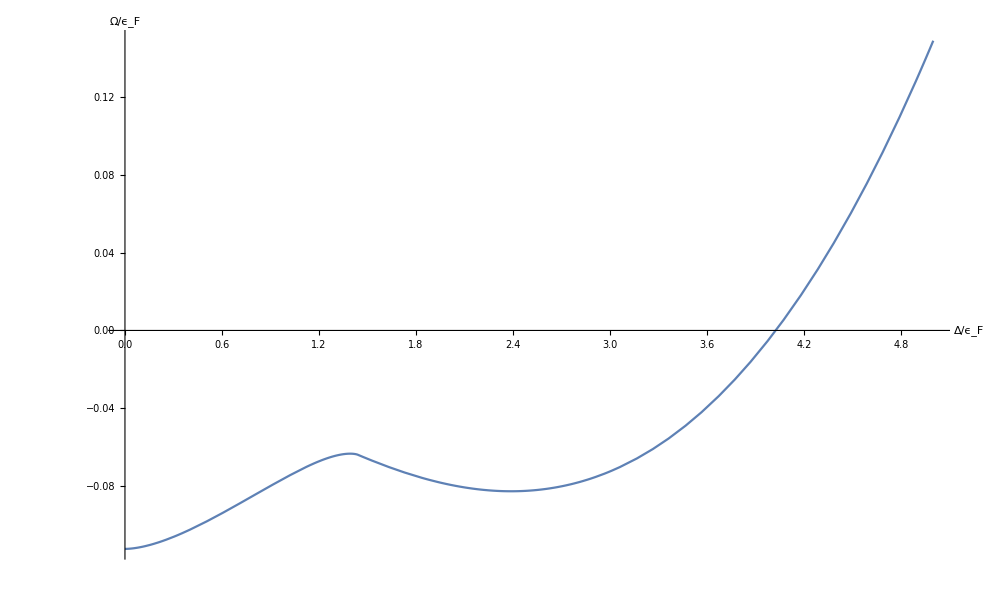

```mathematica
(*Thermaldynamical Potential*)
ClearAll["Global`*"];
t=1;
r=0.5;
ϵ[k_]:=k^2;
ϵn[k_,r_]:=ϵ[k]*(r-1)/(r+1);
ξ[k_,μ_]:=ϵ[k]-μ;
Ek[k_,μ_,Δ_]:=Sqrt[ξ[k,μ]^2+Δ^2];
E1[k_,μ_,Δ_,h_,r_]:=Ek[k,μ,Δ]-(h-ϵn[k,r]);
E2[k_,μ_,Δ_,h_,r_]:=Ek[k,μ,Δ]+(h-ϵn[k,r]);
T1[k_,μ_,Δ_,h_,r_]:=If[E1[k,μ,Δ,h,r]<0,1,0];
T2[k_,μ_,Δ_,h_,r_]:=If[E2[k,μ,Δ,h,r]<0,1,0];
Ω0[μ_,Δ_]:=NIntegrate[Δ^2/2+k^2ξ[k,μ]-k^2 Ek[k,μ,Δ],{k,0,10}];
Ω1[μ_,Δ_,h_,r_]:=NIntegrate[k^2(E1[k,μ,Δ,h,r]*T1[k,μ,Δ,h,r]+E2[k,μ,Δ,h,r]*T2[k,μ,Δ,h,r]),{k,-10,10}];
Ω[μ_,Δ_,h_,r_,t_]:=-Δ^2 t/(8 Pi)+(1/(2 Pi^2))(Ω0[μ,Δ]+Ω1[μ,Δ,h,r]);
μ0=1;
h0=1.44;
tt=TextString[t]//InputForm;
Plot[Ω[μ0,Δ,h0,t,r],{Δ,0,5},AxesLabel->{"Δ/ϵ_F","Ω/ϵ_F"}]
```

NIntegrate::inumr: The integrand k^2\ (1.  + k^2) + Δ^2/2 - k^2\ √(1.  + k^2)^2 + Δ^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 5}}.

NIntegrate::inumr: The integrand k^2\ ((1.  - 0.333333\ k^2 + √Plus[« 2 »]^2 + Δ^2)\ If[1.  - 0.333333\ Power[« 2 »] + √Plus[« 2 »] < 0, 1, 0] + (-1. + 0.333333\ k^2 + √Plus[« 2 »]^2 + Δ^2)\ If[-1. + 0.333333\ Power[« 2 »] + √Plus[« 2 »] < 0, 1, 0]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 5}}.

NIntegrate::inumr: The integrand k^2\ (1.  + k^2) + Δ^2/2 - k^2\ √(1.  + k^2)^2 + Δ^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 5}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.83544515234142}. NIntegrate obtained 6.49171×10^-10 and 5.64181×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.83544515234142}. NIntegrate obtained 6.49171×10^-10 and 5.64181×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.94748847128778389270475912553592934273183345794677734375}. NIntegrate obtained 6.48539×10^-10 and 6.45458×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum :: lstol will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate :: errprec will be suppressed during this calculation.

FindMinimum::nrnum: The function value 4.39766×10^-17 + -0.0495742 + NIntegrate[Compile`$1/2 + Compile`$220\ ξ[k, -0.4] - Compile`$220\ Ek[« 3 »], {k, 0, 5}]/2\ π^2 is not a real number at {Δ} = {-7.43389×10^-8}.

FindMinimum::nrnum: The function value 5.57761×10^-18 + -0.0991484 + NIntegrate[Compile`$1/2 + Compile`$220\ ξ[k, -0.2] - Compile`$220\ Ek[« 3 »], {k, 0, 5}]/2\ π^2 is not a real number at {Δ} = {-2.64746×10^-8}.

General::stop: Further output of FindMinimum :: nrnum will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum :: sdprec will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

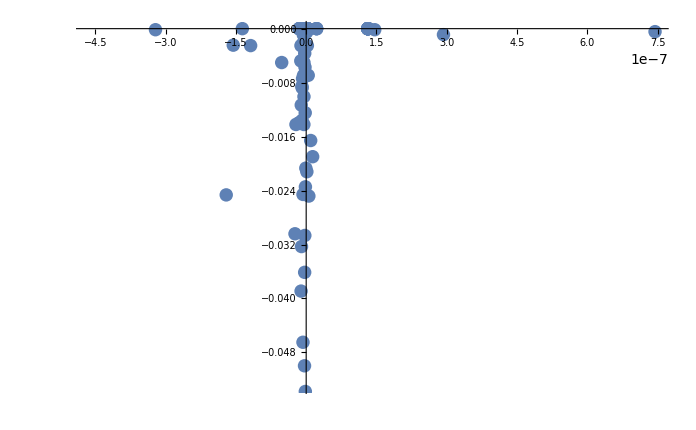

```mathematica
(*Thermaldynamical Potential*)
ClearAll["Global`*"];
t=-0.1;
r=0.5;
ϵ[k_]:=k^2;
ϵn[k_]:=ϵ[k]*(r-1)/(r+1);
ξ[k_,μ_]:=ϵ[k]-μ;
Ek[k_,μ_,Δ_]:=Sqrt[ξ[k,μ]^2+Δ^2];
E1[k_,μ_,Δ_,h_]:=Ek[k,μ,Δ]-(h-ϵn[k]);
E2[k_,μ_,Δ_,h_]:=Ek[k,μ,Δ]+(h-ϵn[k]);
T1[k_,μ_,Δ_,h_]:=If[E1[k,μ,Δ,h]<0,1,0];
T2[k_,μ_,Δ_,h_]:=If[E2[k,μ,Δ,h]<0,1,0];
Ω0[μ_,Δ_]:=NIntegrate[Δ^2/2+k^2ξ[k,μ]-k^2 Ek[k,μ,Δ],{k,0,5}];
Ω1[μ_,Δ_,h_]:=NIntegrate[k^2(E1[k,μ,Δ,h]*T1[k,μ,Δ,h]+E2[k,μ,Δ,h]*T2[k,μ,Δ,h]),{k,-5,5}];
Ω[μ_,Δ_,h_]:=-Δ^2 t/(4 Pi)+(1/(2 Pi^2))(Ω0[μ,Δ]+Ω1[μ,Δ,h]);
finddelta[μ0_,h0_]:=Module[{μ=μ0,h=h0},{Δ/.FindMinimum[Ω[μ,Δ,h],{Δ,0.5}][[2]],FindMinimum[Ω[μ,Δ,h],{Δ,0.5}][[1]]}];
Ωtest[μ0_,h0_]:=finddelta[μ0,h0][[2]];
data=Table[{Δ/.FindMinimum[Ω[μ0,Δ,h0],{Δ,0.5}][[2]],FindMinimum[Ω[μ0,Δ,h0],{Δ,0.5}][[1]]},{μ0,-1,1,0.2},{h0,-1,1,0.2}];
ListPlot[Flatten[data,1]]
```

```mathematica
data
```

{{{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16},{1.31565×10^-7,5.21765×10^-16}},{{1.32601×10^-9,-0.000156966},{2.61263×10^-9,8.8153×10^-20},{2.61263×10^-9,8.8153×10^-20},{2.61263×10^-9,8.8153×10^-20},{2.61263×10^-9,8.8153×10^-20},{2.61263×10^-9,8.8153×10^-20},{2.61263×10^-9,8.8153×10^-20},{2.61263×10^-9,8.8153×10^-20},{2.61263×10^-9,8.8153×10^-20},{2.61263×10^-9,8.8153×10^-20},{1.60816×10^-9,-0.000443967}},{{-4.96934×10^-9,-0.000887934},{-4.31545×10^-9,-0.000156966},{-8.53935×10^-9,1.72859×10^-18},{-8.53935×10^-9,1.72859×10^-18},{-8.53935×10^-9,1.72859×10^-18},{-8.53935×10^-9,1.72859×10^-18},{-8.53935×10^-9,1.72859×10^-18},{-8.53935×10^-9,1.72859×10^-18},{-8.53935×10^-9,1.72859×10^-18},{-2.79169×10^-9,-0.000443967},{-9.13823×10^-9,-0.00251146}},{{-7.20404×10^-9,-0.00244686},{2.92978×10^-7,-0.000887934},{-3.21591×10^-7,-0.000156966},{-1.45533×10^-8,5.01906×10^-18},{-1.45533×10^-8,5.01906×10^-18},{-1.45533×10^-8,5.01906×10^-18},{-1.45533×10^-8,5.01906×10^-18},{-1.45533×10^-8,5.01906×10^-18},{-4.13633×10^-9,-0.000443967},{-1.18569×10^-7,-0.00251146},{-2.68876×10^-10,-0.00692076}},{{-5.2251×10^-8,-0.00502292},{-1.55618×10^-7,-0.00244686},{-6.17562×10^-9,-0.000887934},{-6.55214×10^-7,-0.000156966},{2.22125×10^-8,9.62632×10^-18},{2.22125×10^-8,9.62632×10^-18},{2.22125×10^-8,9.62632×10^-18},{7.4449×10^-7,-0.000443967},{-1.11275×10^-8,-0.00251146},{4.34933×10^-9,-0.00692076},{-2.17927×10^-8,-0.0142069}},{{-8.60048×10^-9,-0.00877467},{-4.74756×10^-9,-0.00502292},{-7.49054×10^-9,-0.00244686},{-4.97356×10^-9,-0.000887934},{1.46289×10^-7,-0.000156966},{-1.36229×10^-7,-1.11247×10^-16},{-6.26005×10^-9,-0.000443967},{2.52764×10^-9,-0.00251146},{-5.68388×10^-9,-0.00692076},{-4.9092×10^-9,-0.0142069},{5.69454×10^-9,-0.0248185}},{{-8.86107×10^-9,-0.0135999},{-9.12424×10^-9,-0.00853301},{-1.1494×10^-8,-0.00478125},{-7.10646×10^-9,-0.00220519},{-6.62637×10^-10,-0.000646269},{0.100741,-0.000297841},{0.0000102603,-0.00226979},{-1.01575×10^-9,-0.00667909},{-1.564×10^-8,-0.0139653},{-6.78095×10^-9,-0.0245769},{-1.08935×10^-8,-0.0389081}},{{1.38119×10^-8,-0.0189823},{-2.05864×10^-9,-0.0124745},{-7.73135×10^-9,-0.0074076},{-3.09218×10^-9,-0.00365585},{0.240138,-0.00181594},{0.240138,-0.00181594},{-2.5313×10^-9,-0.00571066},{0.0000486378,-0.0128399},{-1.63491×10^-9,-0.0234515},{-1.08723×10^-6,-0.0377827},{-3.50324×10^-8,-0.0561896}},{{-1.70629×10^-7,-0.0246467},{9.60922×10^-9,-0.0165822},{-4.73423×10^-9,-0.0100743},{0.384495,-0.00517329},{0.384495,-0.00517329},{0.384495,-0.00517329},{-1.05125×10^-8,-0.0113277},{1.45131×10^-9,-0.0212083},{-0.0000306865,-0.0353826},{-1.81546×10^-9,-0.0537895},{-1.2086×10^-9,-0.0765995}},{{-2.38944×10^-8,-0.0304095},{-7.80296×10^-10,-0.0206806},{0.528987,-0.0108026},{0.528987,-0.0108026},{0.528987,-0.0108026},{0.528987,-0.0108026},{0.528987,-0.0108026},{-1.00042×10^-8,-0.0323044},{-3.55186×10^-9,-0.0499803},{0.0000406831,-0.0726334},{-8.26049×10^-9,-0.100151}},{{-3.24095×10^-9,-0.0361276},{0.672013,-0.0190433},{0.672013,-0.0190433},{0.672013,-0.0190433},{0.672013,-0.0190433},{0.672013,-0.0190433},{-2.89676×10^-9,-0.0306632},{-6.85213×10^-9,-0.0464941},{7.7552×10^-9,-0.0677451},{-8.31204×10^-9,-0.0945315},{0.000052753,-0.126885}}}

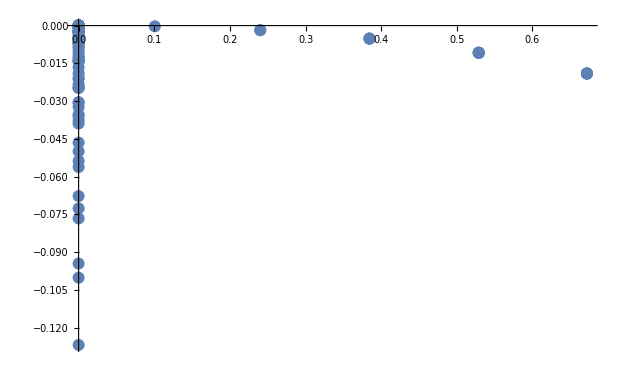

```mathematica
data2=Flatten[data,1];
ListPlot[data2,PlotRange->Full]
```